{{0.,255.43},{0.05,240.44},{0.1,204.72},{0.15,194.86},{0.2,191.32},{0.25,177.45},{0.3,155.23},{0.35,151.3},{0.4,129.89},{0.45,127.73},{0.5,114.91},{0.55,106.21},{0.6,101.1},{0.65,89.24},{0.7,82.47},{0.75,83.45},{0.8,74.83},{0.85,68.44},{0.9,61.65},{0.95,58.19},{1.,55.45},{1.05,52.3},{1.1,48.88},{1.15,45.75},{1.2,42.1},{1.25,39.1},{1.3,36.},{1.35,32.87},{1.4,28.51},{1.45,26.47},{1.5,25.86},{1.55,24.79},{1.6,23.21},{1.65,20.36},{1.7,18.52},{1.75,17.82},{1.8,16.27},{1.85,14.95},{1.9,13.64},{1.95,13.29},{2.,12.54},{2.05,11.68},{2.1,9.92},{2.15,9.51},{2.2,8.73},{2.25,7.99},{2.3,7.44},{2.35,7.05},{2.4,6.53},{2.45,5.96},{2.5,5.59},{2.55,5.38},{2.6,4.82},{2.65,4.39},{2.7,4.32},{2.75,4.02},{2.8,3.56},{2.85,3.43},{2.9,3.12},{2.95,2.79},{3.,2.77},{3.05,2.44},{3.1,2.25},{3.15,2.12},{3.2,1.87},{3.25,1.82},{3.3,1.65},{3.35,1.51},{3.4,1.48},{3.45,1.32},{3.5,1.19},{3.55,1.18},{3.6,1.05},{3.65,0.94},{3.7,0.94},{3.75,0.89},{3.8,0.82},{3.85,0.75},{3.9,0.7},{3.95,0.6},{4.,0.58},{4.05,0.56},{4.1,0.49},{4.15,0.47},{4.2,0.43},{4.25,0.4},{4.3,0.38},{4.35,0.33},{4.4,0.31},{4.45,0.28},{4.5,0.27},{4.55,0.24},{4.6,0.23},{4.65,0.22},{4.7,0.2},{4.75,0.18},{4.8,0.17},{4.85,0.16},{4.9,0.15},{4.95,0.13},{5.,0.12},{5.05,0.12},{5.1,0.11},{5.15,0.09},{5.2,0.09},{5.25,0.09},{5.3,0.08},{5.35,0.07},{5.4,0.06},{5.45,0.06},{5.5,0.06},{5.55,0.05},{5.6,0.05},{5.65,0.04},{5.7,0.04},{5.75,0.03},{5.8,0.03},{5.85,0.03},{5.9,0.03},{5.95,0.03},{6.,0.02}}

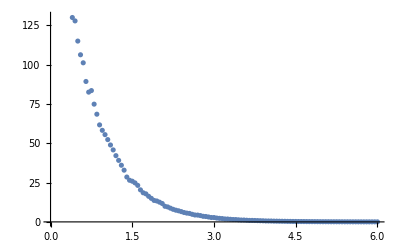

{a→251.707,b→1.52874}

{c→3.27067×10^-11}

{255.43,240.44,204.72,194.86,191.32,177.45,155.23,151.3,129.89,127.73,114.91,106.21,101.1,89.24,82.47,83.45,74.83,68.44,61.65,58.19,55.45,52.3,48.88,45.75,42.1,39.1,36.,32.87,28.51,26.47,25.86,24.79,23.21,20.36,18.52,17.82,16.27,14.95,13.64,13.29,12.54,11.68,9.92,9.51,8.73,7.99,7.44,7.05,6.53,5.96,5.59,5.38,4.82,4.39,4.32,4.02,3.56,3.43,3.12,2.79,2.77,2.44,2.25,2.12,1.87,1.82,1.65,1.51,1.48,1.32,1.19,1.18,1.05,0.94,0.94,0.89,0.82,0.75,0.7,0.6,0.58,0.56,0.49,0.47,0.43,0.4,0.38,0.33,0.31,0.28,0.27,0.24,0.23,0.22,0.2,0.18,0.17,0.16,0.15,0.13,0.12,0.12,0.11,0.09,0.09,0.09,0.08,0.07,0.06,0.06,0.06,0.05,0.05,0.04,0.04,0.03,0.03,0.03,0.03,0.03,0.02}

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

FindFit::fitd: First argument Symbol[] in FindFit is not a list or a rectangular array.

FindFit[Symbol[],a ⅇ^(-b x),{a,b},x]

```mathematica
Remove["Global`*"]
data=Import["/Users/Felix/GitHub/Envariabel-projekt/matserie.dat"]
ListPlot[data]
FindFit[data, a ⅇ^(- b x), {a,b}, x]
FindFit[data,251.70653701301623 ⅇ^(-t/(20000000000 c)) , c,t]
data[[All,2]]
```

```mathematica
Remove["Global`*"]
R=20*10^9;
DSolve[{c*u'[t]+u[t]*(1/R)==0,u[0]==255.43},u[t],t]
```

{{u[t]→255.43 ⅇ^(-t/(20000000000 c))}}

```mathematica
Remove["Global`*"]
R=20*10^9;
DSolve[{u'[t]+u[t]*1/(R*c)==0}, u[t], t]
```

{{u[t]→ⅇ^(-t/(20000000000 c)) C[1]}}

```mathematica
Remove["Global`*"]
Solve[u==255.43 ⅇ^(-t/(20000000000 c)),c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→-(5.×10^-11 t)/Log[0.00391497 u]}}

```mathematica
Remove["Global`*"]
R=500 *10^9
DSolve[{i'[t]+(1/R*C) i[t]==0, i[0.05]==4.8088*10^-10},i[t],t]
```

500000000000

{{i[t]→4.8088×10^-10 ⅇ^(1.×10^-13 C-(C t)/500000000000)}}

```mathematica
Remove["Global`*"]
R=20*10^9;
C0=3.27*10^-11;


D[251.707*ⅇ^(-t/(R*C0))]*C0
```

8.23082×10^-9 ⅇ^(-1.52905 t)

```mathematica
3.27*10^-11
```

8.25599×10^-9 ⅇ^(-1.52439 t)